```mathematica
Exit[]
```

```mathematica
Get[NotebookDirectory[]<>"eoms.wl"];
```

## EOMs and symmetry

```mathematica
Cpullin*κ/(4π)*(√Abs[Ex[x]])/Sign[Eϕ[x]]//FullSimplify
```

1/(2 Eϕ[x]^3)(-4 Conjugate[Eϕ[x]] (Eϕ[x]^3 (1+Kϕ[x]^2)+Ex[x] Ex'[x] Eϕ'[x])+Abs[Eϕ[x]]^2 (Ex'[x]^2+4 Ex[x] (-4 Eϕ[x] Kx[x] Kϕ[x]+Ex''[x])))

```mathematica
mubar={Kx[x]-> Sin[(√Δ √Abs[Ex[x]])/Eϕ[x] 2β Kx[x]]/(2β(√Δ √Abs[Ex[x]])/Eϕ[x]),Kϕ[x]-> Sin[(√Δ)/(√Abs[Ex[x]])β Kϕ[x]]/(β(√Δ)/(√Abs[Ex[x]]))};
```

```mathematica
Hmubar=Cpullin/.κ-> 16π G/.mubar//Expand
```

-Abs[Eϕ[x]]/(2 G √Abs[Ex[x]])-(Abs[Eϕ[x]] Ex[x] Sin[(2 β √Δ √Abs[Ex[x]] Kx[x])/Eϕ[x]] Sin[(β √Δ Kϕ[x])/(√Abs[Ex[x]])])/(G β^2 Δ √Abs[Ex[x]])-(√Abs[Ex[x]] Abs[Eϕ[x]] Sin[(β √Δ Kϕ[x])/(√Abs[Ex[x]])]^2)/(2 G β^2 Δ)+(Abs[Eϕ[x]] Ex'[x]^2)/(8 G √Abs[Ex[x]] Eϕ[x]^2)-(Abs[Eϕ[x]] Ex[x] Ex'[x] Eϕ'[x])/(2 G √Abs[Ex[x]] Eϕ[x]^3)+(Abs[Eϕ[x]] Ex[x] Ex''[x])/(2 G √Abs[Ex[x]] Eϕ[x]^2)

```mathematica
HmubarS1=Hmubar/.Abs[Ex[x]]-> -Ex[x]/.Abs[Eϕ[x]]-> Eϕ[x]
```

-Eϕ[x]/(2 G √(-Ex[x]))-(Ex[x] Eϕ[x] Sin[(2 β √Δ √(-Ex[x]) Kx[x])/Eϕ[x]] Sin[(β √Δ Kϕ[x])/(√(-Ex[x]))])/(G β^2 Δ √(-Ex[x]))-(√(-Ex[x]) Eϕ[x] Sin[(β √Δ Kϕ[x])/(√(-Ex[x]))]^2)/(2 G β^2 Δ)+Ex'[x]^2/(8 G √(-Ex[x]) Eϕ[x])-(Ex[x] Ex'[x] Eϕ'[x])/(2 G √(-Ex[x]) Eϕ[x]^2)+(Ex[x] Ex''[x])/(2 G √(-Ex[x]) Eϕ[x])

```mathematica
HmubarS=Hmubar/.Abs[Ex[x]]-> Ex[x]/.Abs[Eϕ[x]]-> Eϕ[x]
```

-Eϕ[x]/(2 G √Ex[x])-(√Ex[x] Eϕ[x] Sin[(2 β √Δ √Ex[x] Kx[x])/Eϕ[x]] Sin[(β √Δ Kϕ[x])/(√Ex[x])])/(G β^2 Δ)-(√Ex[x] Eϕ[x] Sin[(β √Δ Kϕ[x])/(√Ex[x])]^2)/(2 G β^2 Δ)+Ex'[x]^2/(8 G √Ex[x] Eϕ[x])-(√Ex[x] Ex'[x] Eϕ'[x])/(2 G Eϕ[x]^2)+(√Ex[x] Ex''[x])/(2 G Eϕ[x])

```mathematica
delta[f1_,f2_]:=(D[f1, f2[x]])-D[(D[f1, f2'[x]]), x]+D[D[(D[f1, f2''[x]]), x], x];
varq={Ex,Eϕ};varp={Kx,Kϕ};
poisson[f1_,f2_]:=-G∑_(i=1)^Length[varq] (delta[f1,varq[[i]]]delta[f2,varp[[i]]]-delta[f1,varp[[i]]]delta[f2,varq[[i]]]);
```

```mathematica
addtime={Eϕ[v]-> Eϕ[t,x],Kϕ[v]-> Kϕ[t,x],Ex[v]-> Ex[t,x], Kx[v]->  Kx[t,x],Ex'[v]->D[Ex[t,x], x],Eϕ'[v]-> D[Eϕ[t,x], x],Ex''[v]-> D[D[Ex[t,x], x], x]}/.v->x;
```

```mathematica
effeomop={D[Kx[t,x], t]-poisson[Kx[x],HmubarS1]/.addtime,
D[Kϕ[t,x], t]-poisson[Kϕ[x],HmubarS1]/.addtime,D[Ex[t,x], t]-poisson[Ex[x],HmubarS1]/.addtime,
D[Eϕ[t,x], t]-poisson[Eϕ[x],HmubarS1]/.addtime}//Expand
```

{(√(-Ex[t,x]) Eϕ[t,x])/(4 Ex[t,x]^2)+(Cos[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))] Eϕ[t,x] Kϕ[t,x] Sin[(2 β √Δ √(-Ex[t,x]) Kx[t,x])/Eϕ[t,x]])/(2 β √Δ Ex[t,x])+(Cos[(2 β √Δ √(-Ex[t,x]) Kx[t,x])/Eϕ[t,x]] Kx[t,x] Sin[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))])/(β √Δ)-(Cos[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))] Eϕ[t,x] Kϕ[t,x] Sin[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))])/(2 β √Δ Ex[t,x])-(√(-Ex[t,x]) Eϕ[t,x] Sin[(2 β √Δ √(-Ex[t,x]) Kx[t,x])/Eϕ[t,x]] Sin[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))])/(2 β^2 Δ Ex[t,x])+(√(-Ex[t,x]) Eϕ[t,x] Sin[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))]^2)/(4 β^2 Δ Ex[t,x])-(√(-Ex[t,x]) (Ex^(0,1)[t,x])^2)/(16 Ex[t,x]^2 Eϕ[t,x])-(√(-Ex[t,x]) Ex^(0,1)[t,x] Eϕ^(0,1)[t,x])/(4 Ex[t,x] Eϕ[t,x]^2)+(√(-Ex[t,x]) Ex^(0,2)[t,x])/(4 Ex[t,x] Eϕ[t,x])+Kx^(1,0)[t,x],-(√(-Ex[t,x]))/(2 Ex[t,x])-(2 Cos[(2 β √Δ √(-Ex[t,x]) Kx[t,x])/Eϕ[t,x]] Ex[t,x] Kx[t,x] Sin[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))])/(β √Δ Eϕ[t,x])-(√(-Ex[t,x]) Sin[(2 β √Δ √(-Ex[t,x]) Kx[t,x])/Eϕ[t,x]] Sin[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))])/(β^2 Δ)+(√(-Ex[t,x]) Sin[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))]^2)/(2 β^2 Δ)+(√(-Ex[t,x]) (Ex^(0,1)[t,x])^2)/(8 Ex[t,x] Eϕ[t,x]^2)+Kϕ^(1,0)[t,x],-(2 Cos[(2 β √Δ √(-Ex[t,x]) Kx[t,x])/Eϕ[t,x]] Ex[t,x] Sin[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))])/(β √Δ)+Ex^(1,0)[t,x],(Cos[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))] Eϕ[t,x] Sin[(2 β √Δ √(-Ex[t,x]) Kx[t,x])/Eϕ[t,x]])/(β √Δ)-(Cos[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))] Eϕ[t,x] Sin[(β √Δ Kϕ[t,x])/(√(-Ex[t,x]))])/(β √Δ)+Eϕ^(1,0)[t,x]}

```mathematica
effeomfor={D[Kx[t,x], t],D[Kϕ[t,x], t],D[Ex[t,x], t],D[Eϕ[t,x], t]}-({D[Kx[t,x], t],D[Kϕ[t,x], t],D[Ex[t,x], t],D[Eϕ[t,x], t]}/.(Solve[effeom,{D[Kx[t,x], t],D[Kϕ[t,x], t],D[Ex[t,x], t],D[Eϕ[t,x], t]}]//Flatten))//Expand;
```

```mathematica
transf={Ex[t,x]->- Ex[t,x],Kϕ[t,x]->- Kϕ[t,x],D[D[Ex[t,x], x], x]->- D[D[Ex[t,x], x], x],D[Kx[t,x], t]->- D[Kx[t,x], t],D[Eϕ[t,x], t]-> -D[Eϕ[t,x], t],D[Eϕ[t,x], x]-> -D[Eϕ[t,x], x]};
```

```mathematica
(effeomop[[1]]/.transf)+effeomfor[[1]]
(effeomop[[2]]/.transf)-effeomfor[[2]]
(effeomop[[3]]/.transf)-effeomfor[[3]]
(effeomop[[4]]/.transf)+effeomfor[[4]]
```

0

0

0

«1 more identical outputs»

```mathematica
effeomfor-{D[Kx[t,x], t]-poisson[Kx[x],HmubarS]/.addtime,
D[Kϕ[t,x], t]-poisson[Kϕ[x],HmubarS]/.addtime,D[Ex[t,x], t]-poisson[Ex[x],HmubarS]/.addtime,
D[Eϕ[t,x], t]-poisson[Eϕ[x],HmubarS]/.addtime}//Expand
```

{0,0,0,0}

## Change variables

```mathematica
simpliz={Kϕ[t,x]-> Kϕ[x-t],Kx[t,x]-> Kx[x-t],Eϕ[t,x]-> Eϕ[x-t],Ex[t,x]-> Ex[x-t],D[Kϕ[t,x], t]-> D[Kϕ[x-t], t],D[Kx[t,x], t]-> D[Kx[x-t], t],D[Eϕ[t,x], t]-> D[Eϕ[x-t], t],D[Ex[t,x], t]-> D[Ex[x-t], t],D[Eϕ[t,x], x]-> D[Eϕ[x-t], x],D[Ex[t,x], x]-> D[Ex[x-t], x],D[D[Ex[t,x], x], x]-> D[D[Ex[x-t], x], x]};
```

```mathematica
exprim=(Solve[(effeomop[[3]]/.simpliz/.x->t+z)==0,Ex'[z]]//Flatten)
```

{Ex'[z]→-(2 Cos[(2 β √Δ √(-Ex[z]) Kx[z])/Eϕ[z]] Ex[z] Sin[(β √Δ Kϕ[z])/(√(-Ex[z]))])/(β √Δ)}

```mathematica
effeomop1={((effeomop[[1]]/.simpliz/.x->t+z)/.exprim/.D[exprim, z]),(effeomop[[2]]/.simpliz/.x->t+z),(effeomop[[3]]/.simpliz/.x->t+z),(effeomop[[4]]/.simpliz/.x->t+z)};
```

```mathematica
chvarop0={Kx[z]->(ⅇ^u[z] K1[z])/(√(-Ex[z])),Kϕ[z]->√(-Ex[z]) K2[z],Eϕ[z]->ⅇ^u[z]};
chvarop={chvarop0,D[chvarop0, z]}//Flatten
```

{Kx[z]→(ⅇ^u[z] K1[z])/(√(-Ex[z])),Kϕ[z]→√(-Ex[z]) K2[z],Eϕ[z]→ⅇ^u[z],Kx'[z]→(ⅇ^u[z] K1[z] Ex'[z])/(2 (-Ex[z])^(3/2))+(ⅇ^u[z] K1'[z])/(√(-Ex[z]))+(ⅇ^u[z] K1[z] u'[z])/(√(-Ex[z])),Kϕ'[z]→-(K2[z] Ex'[z])/(2 √(-Ex[z]))+√(-Ex[z]) K2'[z],Eϕ'[z]→ⅇ^u[z] u'[z]}

```mathematica
eomKEuop={K1'[z],K2'[z],Ex'[z],u'[z]}-({K1'[z],K2'[z],Ex'[z],u'[z]}/.(Solve[Thread[(effeomop1/.chvarop)==0],{K1'[z],K2'[z],Ex'[z],u'[z]}]//Flatten))//Simplify//Expand;
```

```mathematica
eomKEuasymop=Series[eomKEuop/.u[z]-> Log[Eϕ[z]],{Eϕ[z],∞,0}]//Normal;
```

```mathematica
transf1={Ex[z]->-Ex[z],K2[z]->-K2[z],Ex'[z]->Ex'[z],K1'[z]->-K1'[z],u'[z]->-u'[z]};
```

```mathematica
(eomKEuop[[1]]/.transf1//Expand)+eomKEu[[1]]//Expand//Simplify
(eomKEuop[[2]]/.transf1//Expand)-eomKEu[[2]]//Expand
(eomKEuop[[3]]/.transf1//Expand)-eomKEu[[3]]//Expand
(eomKEuop[[4]]/.transf1//Expand)+eomKEu[[4]]//Expand
```

0

0

0

«1 more identical outputs»

```mathematica
(eomKEuasymop[[1]]/.transf1//Expand)+eomKEuasym[[1]]//Expand//Simplify
(eomKEuasymop[[2]]/.transf1//Expand)-eomKEuasym[[2]]//Expand
(eomKEuasymop[[3]]/.transf1//Expand)-eomKEuasym[[3]]//Expand
(eomKEuasymop[[4]]/.transf1//Expand)+eomKEuasym[[4]]//Expand
```

0

0

0

«1 more identical outputs»

## Initial condition

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
bdy0={Ex[x0]-> 3/2 (3/2)^(1/3) (√Rs (x0))^(4/3),Eϕ[x0]-> (3/2)^(1/3) √Rs (√Rs (x0))^(1/3),Kx[x0]-> Rs/(3 2^(2/3) 3^(1/3) (√Rs (x0))^(4/3)),Kϕ[x0]-> -((2/3)^(1/3) √Rs)/(√Rs (x0))^(1/3)};bdyKv0=Refine[{K1[z]-> (√Ex[z] Kx[z])/Eϕ[z],K2[z]-> Kϕ[z]/(√Ex[z]),v1[z]-> Log[Ex[z]],v2[z]-> Log[Eϕ[z]]}/.z-> x0/.bdy0,Assumptions->{x0>0,Δ>0,Rs>0}];
bdyKv={K1[z]==K1[x0],K2[z]==K2[x0],v1[z]==v1[x0],v2[z]==v2[x0]}/.bdyKv0/.z-> x0
```

{K1[x0]==1/(6 x0),K2[x0]==-2/(3 x0),v1[x0]==Log[3/2 (3/2)^(1/3) Rs^(2/3) x0^(4/3)],v2[x0]==Log[(3/2)^(1/3) Rs^(2/3) x0^(1/3)]}

## 循环

```mathematica
xM=3*10^8;
m=RandomVariate[NormalDistribution[5,2]];
n=RandomVariate[NormalDistribution[1,0.1]];
```

```mathematica
parameters={a-> 1,β->1,Rs->10^8 n,Δ->0.01m,t0->0,x0-> xM,μ0-> 0.1,λ0-> 0.1};
```

```mathematica
bdyKv/.parameters//N
```

{K1[3.×10^8]==5.55556×10^-10,K2[3.×10^8]==-2.22222×10^-9,v1[3.×10^8]==38.8419,v2[3.×10^8]==18.9172}

```mathematica
mid=-350;
effeomODEKv={Table[eomKv[[i]]==0,{i,1,4}],bdyKv}/.parameters//Flatten;
nsolKv=NDSolve[effeomODEKv,{K1[z],K2[z],v1[z],v2[z]},{z,mid,xM},Method->"ImplicitRungeKutta"]//Flatten
```

{K1[z]→InterpolatingFunction[…][z],K2[z]→InterpolatingFunction[…][z],v1[z]→InterpolatingFunction[…][z],v2[z]→InterpolatingFunction[…][z]}

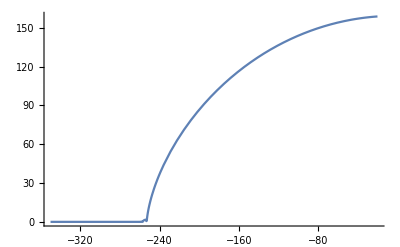

```mathematica
Plot[√(ⅇ^v1[z])/.nsolKv,{z,mid,-20},PlotRange->All]
```

```mathematica
newbdy={ K1[z1]->K1[z] , K2[z1]-> K2[z],Ex[z]->ⅇ^v1[z],Eϕ[z]->ⅇ^v2[z]}/.nsolKv/.z-> mid/.z1-> mid
```

{K1[-350]→2.95809,K2[-350]→-2.21173,Ex[-350]→0.0879933,Eϕ[-350]→5.91205×10^64}

```mathematica
bdyKu={K1[z]== K1[x0],K2[z]== K2[x0],u[z]==Log[Eϕ[x0]],Ex[z]== Ex[x0]}/.x0->mid/.newbdy/.z-> mid
```

{K1[-350]==2.95809,K2[-350]==-2.21173,u[-350]==149.142,Ex[-350]==0.0879933}

```mathematica
bdyKu1={K1[z]->  K1[x0],K2[z]->  K2[x0],Ex[z]->  Ex[x0]}/.x0->mid/.newbdy
```

{K1[z]→2.95809,K2[z]→-2.21173,Ex[z]→0.0879933}

```mathematica
asymp=eomKEuasym/.{K1'[z]->0,K2'[z]->0}/.parameters/.bdyKu1
```

{-4.70735×10^-14,6.21725×10^-14,1.36378×10^-15+Ex'[z],1.39821+u'[z]}

```mathematica
uns=DSolve[{asymp[[4]]==0,bdyKu[[3]]},u[z],z]//Expand//Flatten
```

{u[z]→-340.23-1.39821 z}

```mathematica
nsolutionODEKu={bdyKu1,uns,K1'[z]->0,K2'[z]->0,Ex'[z]->0,Ex''[z]->0}//Flatten
```

{K1[z]→2.95809,K2[z]→-2.21173,Ex[z]→0.0879933,u[z]→-340.23-1.39821 z,K1'[z]→0,K2'[z]→0,Ex'[z]→0,Ex''[z]→0}

```mathematica
eomKEuasym/.nsolutionODEKu/.D[nsolutionODEKu, z]/.parameters
```

{-4.79616×10^-14,6.21725×10^-14,1.36378×10^-15,0.}

```mathematica
eomKv/.{v1[z]->Log[Ex[z]],v2[z]->u[z]}/.D[{v1[z]->Log[Ex[z]],v2[z]->u[z]}, z]/.nsolutionODEKu/.D[nsolutionODEKu, z]/.parameters/.z-> mid
```

{-4.79616×10^-14,6.21725×10^-14,1.54987×10^-14,0.}

## initial condition in the new patch

```mathematica
ini={u[z0]->( u[z]/.nsolutionODEKu/.z-> -z0),Ex[z0]-> -(Ex[z]/.nsolutionODEKu/.z-> -xM)}
```

{u[z0]→-340.23+1.39821 z0,Ex[z0]→-0.0879933}

```mathematica
reduce=eomKEuasymop/.({D[ini[[1]], z0],ini[[2]],Ex'[z]->0}/.z0->z)/.{K2[z]-> kk2/(β √Δ),K1[z]-> kk1/(2 β √Δ)}/.parameters;
```

```mathematica
solveK1K20=Solve[{reduce[[3]]==0,reduce[[4]]==0},{kk1,kk2},Method->Reduce];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(({kk1,kk2}/.solveK1K20)-({kk1,kk2}/.solveK1K20/.{C[1]->0,C[2]->0}))/(2π)//Chop
```

{{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]},{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]},{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]},{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]},{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]},{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]},{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]},{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]},{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]},{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]},{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]},{ConditionalExpression[1. C[1],C[1]∈ℤ],ConditionalExpression[1. C[2],C[2]∈ℤ]}}

```mathematica
solveK1K2=solveK1K20/.{C[1]->0,C[2]->0}
```

{{kk1→-1.5708,kk2→-2.55436},{kk1→-1.5708,kk2→1.75918},{kk1→-1.5708,kk2→-1.17321-0.776394 ⅈ},{kk1→-1.5708,kk2→-1.17321+0.776394 ⅈ},{kk1→1.5708,kk2→-1.38241},{kk1→1.5708,kk2→0.587233},{kk1→1.5708,kk2→1.96838+0.776394 ⅈ},{kk1→1.5708,kk2→1.96838-0.776394 ⅈ},{kk1→-0.380339,kk2→3.14159},{kk1→2.76125,kk2→0.},{kk1→0.380339,kk2→0.},{kk1→-2.76125,kk2→3.14159}}

```mathematica
Table[reduce0=reduce/.solveK1K2[[i]]/.{K1'[z]->0,K2'[z]->0}//Chop;
If[reduce0[[1]]==0&&reduce0[[2]]==0,l=i,0],{i,1,Length[solveK1K2]}]
```

{0,0,0,0,0,6,0,0,0,0,0,0}

```mathematica
{K1[z]-> kk1/(2 β √Δ),K2[z]-> kk2/(β √Δ)}/.solveK1K2[[l]]/.parameters
```

{K1[z]→2.95809,K2[z]→2.21173}

```mathematica
nsolutionODEKu
```

{K1[z]→2.95809,K2[z]→-2.21173,Ex[z]→0.0879933,u[z]→-340.23-1.39821 z,K1'[z]→0,K2'[z]→0,Ex'[z]→0,Ex''[z]→0}

```mathematica
transf1
```

{Ex[z]→-Ex[z],K2[z]→-K2[z],Ex'[z]→Ex'[z],K1'[z]→-K1'[z],u'[z]→-u'[z]}

```mathematica
({K1[z],-K2[z]}/.{K1[z]-> kk1/(2 β √Δ),K2[z]-> kk2/(β √Δ)}/.solveK1K2[[l]]/.parameters)-({K1[z],K2[z]}/.nsolutionODEKu)//Chop
```

{0,0}

## Chaos

```mathematica
pertrev={K1[t,x]->k1 (1+ϵ c1[t,x]),K2[t,x]->-k2 (1+ϵ c2[t,x]),Ex[t,x]->-ex (1+ϵ p1[t,x]),Eϕ[t,x]->ⅇ^(-a+b (-t+x)) (1+ϵ p2[t,x])};(* ⅇ^(-a+b (-t+x))= r0 ⅇ^(-α1+α0^-1(x-t)) *)
```

```mathematica
numer={k1->(K1[z]/.nsolutionODEKu),k2-> (K2[z]/.nsolutionODEKu),ex-> (Ex[z]/.nsolutionODEKu),a->-(u[z]/.nsolutionODEKu/.z-> 0),b-> -D[(u[z]/.nsolutionODEKu), z]}
```

{k1→2.95809,k2→-2.21173,ex→0.0879933,a→340.23,b→1.39821}

```mathematica
eomop={Derivative[1,0][Kx][t,x],Derivative[1,0][Kϕ][t,x],Derivative[1,0][Ex][t,x],Derivative[1,0][Eϕ][t,x]}-({Derivative[1,0][Kx][t,x],Derivative[1,0][Kϕ][t,x],Derivative[1,0][Ex][t,x],Derivative[1,0][Eϕ][t,x]}/.(Solve[Thread[effeomop==0],{Derivative[1,0][Kx][t,x],Derivative[1,0][Kϕ][t,x],Derivative[1,0][Ex][t,x],Derivative[1,0][Eϕ][t,x]}]//Flatten));
```

```mathematica
eom2=eomop/.{Kx[t,x]->(Eϕ[t,x] K1[t,x])/(√(-Ex[t,x])),Kϕ[t,x]->√(-Ex[t,x]) K2[t,x]}/.D[{Kx[t,x]->(Eϕ[t,x] K1[t,x])/(√(-Ex[t,x])),Kϕ[t,x]->√(-Ex[t,x]) K2[t,x]}, t]/.D[{Kx[t,x]->(Eϕ[t,x] K1[t,x])/(√(-Ex[t,x])),Kϕ[t,x]->√(-Ex[t,x]) K2[t,x]}, x];
```

```mathematica
expandrev=(Series[(eom2//Expand)/.pertrev/.D[pertrev, t]/.D[pertrev, x]/.D[D[pertrev, x], x],{ϵ,0,1}]//Simplify)//Normal;
```

```mathematica
expandrev/.ϵ->0/.numer/.parameters
```

{-2.33803×10^-13 ⅇ^(-340.23-1.39821 t+1.39821 x),-1.36048×10^-14,-1.36378×10^-15,0.}

```mathematica
firstorderrev=D[expandrev, ϵ];
```

```mathematica
eqrev=({firstorderrev[[1]]/(1/(8 ex^(3/2) β^2 Δ)ⅇ^(-a+b (-t+x))),firstorderrev[[2]]/(1/(4 √ex β^2 Δ)),firstorderrev[[3]]/ex,firstorderrev[[4]]/(1/(β √Δ)ⅇ^(-a+b (-t+x)))}//Simplify);
```

```mathematica
solcrev=Solve[{eqrev[[3]]==0,eqrev[[4]]==0},{c1[t,x],c2[t,x]}]//Flatten;
```

```mathematica
solcrev/.numer/.parameters//Expand//Chop
```

{c1[t,x]→-0.152536 p1^(1,0)[t,x],c2[t,x]→0.480946 p2^(1,0)[t,x]}

```mathematica
eqrev2=Series[(eqrev/.solcrev/.D[solcrev, t]/.D[solcrev, x])/.ⅇ^(2 (a+b (t-x)))->s,{s,0,0}]/.numer/.parameters//Normal//Expand
```

{0.-0.140989 p1[t,x]-3.41394×10^-15 p2[t,x]+0.0313077 p1^(1,0)[t,x]+0.201672 p2^(1,0)[t,x]-0.0223913 p1^(2,0)[t,x]-1.47264×10^-16 p2^(2,0)[t,x],0.-0.140989 p1[t,x]+0.100836 p1^(1,0)[t,x]-0.0369033 p2^(1,0)[t,x]+7.3632×10^-17 p1^(2,0)[t,x]+0.0263933 p2^(2,0)[t,x],0.-1.57772×10^-30 p2^(1,0)[t,x],0.-1.4013×10^-45 p1[t,x]-9.86076×10^-32 p1^(1,0)[t,x]-5.55112×10^-17 p2^(1,0)[t,x]}

```mathematica
solprev=DSolve[{eqrev2[[1]]==0,eqrev2[[2]]==0},{p1[t,x],p2[t,x]},{t,x}]//Flatten//Chop//Expand
```

{p1[t,x]→0.845318 ⅇ^(1.39821 t) C[1][x]+0.154682 ⅇ^(0.699103 t) Cos[6.34177 t] C[1][x]-0.203424 ⅇ^(0.699103 t) Sin[6.34177 t] C[1][x]+0.157685 ⅇ^(0.699103 t) Sin[6.34177 t] C[2][x]+0.221258 ⅇ^(1.39821 t) C[4][x]-0.221258 ⅇ^(0.699103 t) Cos[6.34177 t] C[4][x]-0.024391 ⅇ^(0.699103 t) Sin[6.34177 t] C[4][x],p2[t,x]→-0.291431 C[1][x]+0.422659 ⅇ^(1.39821 t) C[1][x]-0.131228 ⅇ^(0.699103 t) Cos[6.34177 t] C[1][x]-0.0787198 ⅇ^(0.699103 t) Sin[6.34177 t] C[1][x]-0.0938544 C[2][x]+0.0938544 ⅇ^(0.699103 t) Cos[6.34177 t] C[2][x]-0.0103463 ⅇ^(0.699103 t) Sin[6.34177 t] C[2][x]+1. C[3][x]-0.110629 C[4][x]+0.110629 ⅇ^(1.39821 t) C[4][x]+0.133294 ⅇ^(0.699103 t) Sin[6.34177 t] C[4][x]}

```mathematica
solrev={solprev,((solcrev/.numer/.parameters//Expand//Chop)/.solprev/.D[solprev, t])}//Flatten;
```

```mathematica
λ=-D[(u[z]/.nsolutionODEKu), z]
```

1.39821

```mathematica
Limit[{p1[t,x]/ⅇ^(λ t),p2[t,x]/ⅇ^(λ t),c1[t,x]/ⅇ^(λ t),c2[t,x]/ⅇ^(λ t)}/.solrev//Expand//Chop,t-> ∞]
```

{0.845318 C[1][x]+0.221258 C[4][x],0.422659 C[1][x]+0.110629 C[4][x],-0.180287 C[1][x]-0.0471892 C[4][x],0.284222 C[1][x]+0.0743937 C[4][x]}